```mathematica
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

Create symbols for each resource function:

```mathematica
CreateResourceFunctionSymbols[]
```

Success[…]

Use a resource function as a symbol:

```mathematica
RF`BirdSay["neat"]
```

neat

### Scope

Specify the context:

```mathematica
CreateResourceFunctionSymbols["MyContext`"]
```

Success[…]

Use a resource function from the new context:

```mathematica
MyContext`PartyParrot["Birdnardo"]
```

-Graphics-

Define a single resource function:

```mathematica
CreateResourceFunctionSymbols["BirdStuff`","BirdSay"]
```

Success[…]

```mathematica
BirdStuff`BirdSay["neat"]
```

neat

Define a specific set of resource functions:

```mathematica
CreateResourceFunctionSymbols["NewContext`",{"PartyParrot","SpeechBubble"}]
```

Success[…]

```mathematica
NewContext`SpeechBubble[NewContext`PartyParrot["Birdnardo"], "I'm the new BirdSay", Scaled[.25]]
```

-Graphics-

List symbols created by CreateResourceFunctionSymbols:

```mathematica
CreateResourceFunctionSymbols["NewContext`",All,"List"]
```

{NewContext`PartyParrot,NewContext`SpeechBubble}

Other symbols are not included in this list:

```mathematica
NewContext`MyFunction[x_]:=x+1;
```

```mathematica
CreateResourceFunctionSymbols["NewContext`",All,"List"]
```

{NewContext`PartyParrot,NewContext`SpeechBubble}

Compare to Names:

```mathematica
Names["NewContext`*"]
```

{NewContext`MyFunction,NewContext`PartyParrot,NewContext`SpeechBubble}

Remove symbols created by CreateResourceFunctionSymbols:

```mathematica
CreateResourceFunctionSymbols["NewContext`",All,"Remove"]
```

Success[…]

Other symbols are not removed:

```mathematica
Names["NewContext`*"]
```

{NewContext`MyFunction}

### Options

#### OverwriteTarget

By default, existing symbols with definitions won't be redefined:

```mathematica
EmptyContext`BirdSay[expr_]:=ResourceFunction["SpeechBubble"][Show[LinguisticAssistant, ImageSize -> 75], expr, Scaled[.25]];
```

```mathematica
res=CreateResourceFunctionSymbols["EmptyContext`",{"BirdSay","PartyParrot","SpeechBubble"}]
```

Success[…]

```mathematica
res["Exists"]
```

{Missing[SymbolExists,EmptyContext`BirdSay]}

The definition is unchanged:

```mathematica
EmptyContext`BirdSay["neat"]
```

-Graphics-neat

Overwrite any existing symbols:

```mathematica
CreateResourceFunctionSymbols["EmptyContext`",{"BirdSay","PartyParrot","SpeechBubble"},OverwriteTarget->True]
```

Success[…]

```mathematica
EmptyContext`BirdSay["neat"]
```

neat

#### ExcludedContexts

By default, some contexts are protected:

```mathematica
CreateResourceFunctionSymbols["System`","ContainsQ"]
```

CreateResourceFunctionSymbols::exctx: Cannot set definitions in excluded context System`.

Failure[…]

Override this protection (at your own risk):

```mathematica
CreateResourceFunctionSymbols["System`","ContainsQ",ExcludedContexts->None]
```

Success[…]

```mathematica
ContainsQ[x+y^z,Power[_,_]]
```

True

```mathematica
ContainsQ[x+y^z,Times[_,_]]
```

False

#### AllowUnknownNames

By default, CreateResourceFunctionSymbol will allow defining symbols for names that are not recognized:

```mathematica
CreateResourceFunctionSymbols["MyContext`","DoesNotExist"]
```

Success[…]

These symbols will fail at run-time if used before the corresponding ResourceFunction exists:

```mathematica
MyContext`DoesNotExist
```

ResourceObject::notfname: The ResourceObject DoesNotExist could not be found.

CreateResourceFunctionSymbols::loadfail: Failed to retrieve definitions for the resource function DoesNotExist.

Failure[…]

Use "AllowUnknownNames"->False to ensure that unrecognized names will cause a failure:

```mathematica
CreateResourceFunctionSymbols["MyContext`","AlsoDoesNotExist","AllowUnknownNames"->False]
```

CreateResourceFunctionSymbols::unkname: AlsoDoesNotExist is not a known resource function name.

Failure[…]

### Applications

Define all resource functions from a particular category:

```mathematica
CreateResourceFunctionSymbols["WFP`",{{"[◼]", "CategoryResourceFunctions"}}["Wolfram Physics Project","Name"]]
```

Success[…]

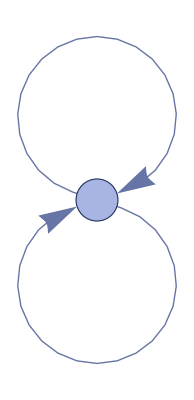
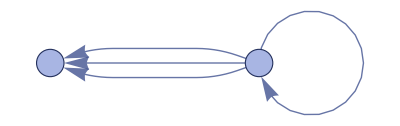
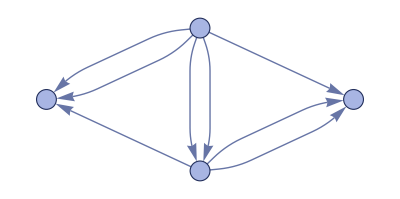
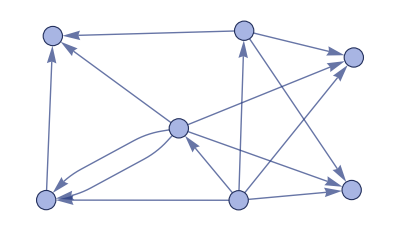
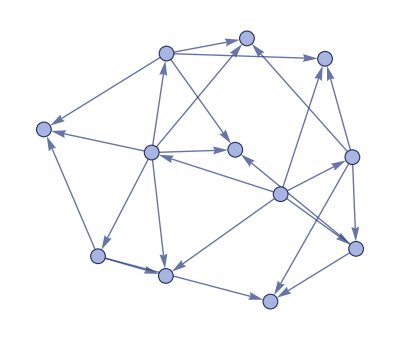
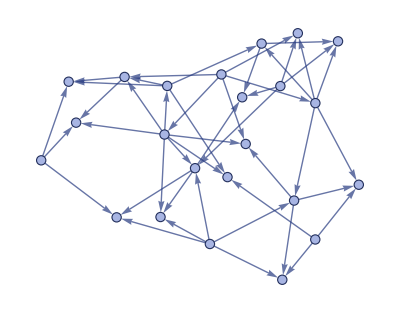

```mathematica
WFP`WolframModel[{{x,y},{x,z}}->{{x,z},{x,w},{y,w},{z,w}},{{0,0},{0,0}},5,"StatesPlotsList"]
```

```mathematica
WFP`GraphReconstructedSurface[WFP`WolframModel[,{{0,0},{0,0}},10,"FinalState"]]
```

-Graphics3D-

Create symbols in the current context to reference resource functions by their base name:

```mathematica
CreateResourceFunctionSymbols[$Context];
```

```mathematica
FoldRight[f,x,{a,b,c,d}]
```

f[a,f[b,f[c,f[d,x]]]]

```mathematica
Stereogram3D[ResourceData["Stanford Bunny","MeshRegion"],Boxed->True]
```

-Graphics-

```mathematica
StringFunction[Subsets]["string"]
```

{,s,t,r,i,n,g,st,sr,si,sn,sg,tr,ti,tn,tg,ri,rn,rg,in,ig,ng,str,sti,stn,stg,sri,srn,srg,sin,sig,sng,tri,trn,trg,tin,tig,tng,rin,rig,rng,ing,stri,strn,strg,stin,stig,stng,srin,srig,srng,sing,trin,trig,trng,ting,ring,strin,strig,strng,sting,sring,tring,string}

### Properties and Relations

Get the list of created symbols:

```mathematica
res=CreateResourceFunctionSymbols["RedefineTest`",{"BirdSay","PartyParrot"}]
```

Success[…]

```mathematica
res["Created"]
```

{RedefineTest`BirdSay,RedefineTest`PartyParrot}

Symbols that have already been created by CreateResourceFunctionSymbols are returned as Missing objects:

```mathematica
res=CreateResourceFunctionSymbols["RedefineTest`",{"BirdSay","PartyParrot","SpeechBubble"}]
```

Success[…]

```mathematica
res["Exists"]
```

{Missing[SymbolExists,RedefineTest`BirdSay],Missing[SymbolExists,RedefineTest`PartyParrot]}

```mathematica
res["Created"]
```

{RedefineTest`SpeechBubble}

User-created resource functions will also be included if they are discoverable by name:

```mathematica
DefineResourceFunction[#+1&,"AddOne"]
```

[◼] | AddOne

```mathematica
CreateResourceFunctionSymbols[];
```

```mathematica
RF`AddOne[5]
```

6

Create a resource function symbol:

```mathematica
CreateResourceFunctionSymbols["DefinitionExample`","GrayCode"]
```

Success[…]

Check the definition:

```mathematica
Definition[DefinitionExample`GrayCode]
```

DefinitionExample`GrayCode:=With[{f$=ResourceFunction[GrayCode,Function]},If[FailureQ[f$],ResourceFunction[MessageFailure][CreateResourceFunctionSymbols::loadfail,GrayCode],Clear[DefinitionExample`GrayCode];DefinitionExample`GrayCode/;(CreateResourceFunctionSymbols;True)=f$]]

The definition changes after the symbol is used for the first time:

```mathematica
DefinitionExample`GrayCode[14]
```

{1,0,0,1}

```mathematica
Definition[DefinitionExample`GrayCode]//InputForm//ToString
```

DefinitionExample`GrayCode /; (CreateResourceFunctionSymbols; True) = FunctionRepository`$6c2750db6e7a4e7b83385739b0a46fd7`GrayCode

### Possible Issues

Locked symbols cannot be overwritten:

```mathematica
AnotherContext`BirdSay="nope";
SetAttributes[AnotherContext`BirdSay,Locked];
```

```mathematica
res=CreateResourceFunctionSymbols["AnotherContext`",{"BirdSay","PartyParrot","SpeechBubble"},OverwriteTarget->True]
```

CreateResourceFunctionSymbols::locked: Cannot set definitions for locked symbol AnotherContext`BirdSay.

Failure[…]

```mathematica
res["Created"]
```

{AnotherContext`PartyParrot,AnotherContext`SpeechBubble}

```mathematica
res["Failed"]
```

{Failure[…]}

### Neat Examples